```mathematica
FullSimplify[Normalize[D[{x,x^2},x]].Normalize[D[{1,0},x]],x∈Reals]
```

0

```mathematica
FullSimplify[Normalize[D[{x,x^2},x]].Normalize[D[{x,1},x]],x∈Reals]
```

1/(√(1+4 x^2))

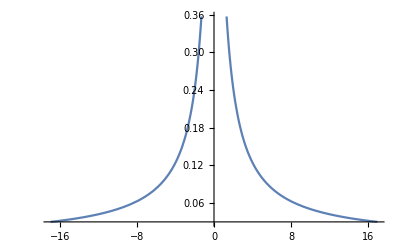

```mathematica
Plot[1/(√(1+4 x^2)),{x,-16.986666666666668,16.986666666666668}]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^2},x],x∈Reals]
```

2/((1+4 x^2)^(3/2))

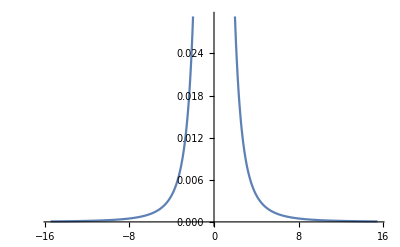

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-15.469999999999999,15.469999999999999}]
```

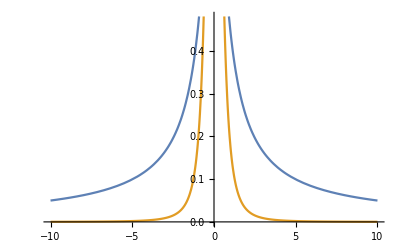

```mathematica
Plot[{1/(√(1+4 x^2)),2/((1+4 x^2)^(3/2))},{x,-10,10}]
```

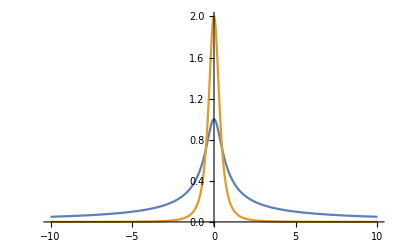

```mathematica
Plot[{1/(√(1+4 x^2)),2/((1+4 x^2)^(3/2))},{x,-10,10},PlotRange->Full]
```

```mathematica
Integrate[2/((1+4 x^2)^(3/2)),{x,-∞,∞}]
```

2

```mathematica
Integrate[1/(√(1+4 x^2)),{x,-∞,∞}]
```

Integrate::idiv: Integral of 1/(√(1+4 x^2)) does not converge on {-∞,∞}.

∫_(-∞)^∞ 1/(√(1+4 x^2))ⅆx

```mathematica
NIntegrate[1/(√(1+4 x^2)),{x,-∞,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.13224×10^28}. NIntegrate obtained 23558.8 and 19651.7 for the integral and error estimates.

23558.8

```mathematica
D[1/(√(1+4 x^2)),x]
```

-(4 x)/((1+4 x^2)^(3/2))

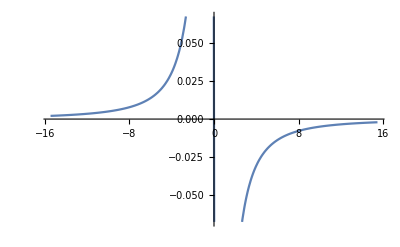

```mathematica
Plot[-(4 x)/((1+4 x^2)^(3/2)),{x,-15.469999999999999,15.469999999999999}]
```

```mathematica
Integrate[1/(√(1+4 x^2)),x]
```

1/2 ArcSinh[2 x]

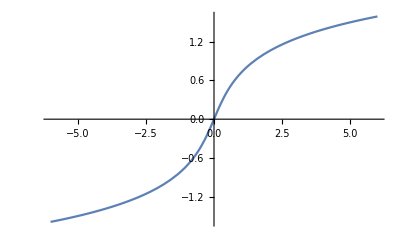

```mathematica
Plot[1/2 ArcSinh[2 x],{x,-6.,6.}]
```

```mathematica
Integrate[2/((1+4 x^2)^(3/2)),x]
```

(2 x)/(√(1+4 x^2))

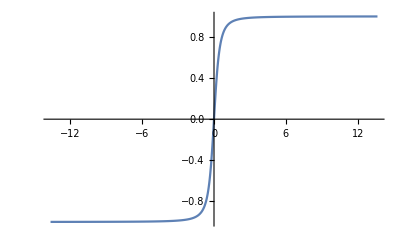

```mathematica
Plot[(2 x)/(√(1+4 x^2)),{x,-13.649999999999999,13.649999999999999}]
```

```mathematica
Cross[{x,x^2,0},{x,x,0}]
```

{0,0,x^2-x^3}

```mathematica
D[{x,x^2,0},x]
```

{1,2 x,0}

```mathematica
Normalize@{1,2 x,0}
```

{1/(√(1+4 Abs[x]^2)),(2 x)/(√(1+4 Abs[x]^2)),0}

```mathematica
Normalize@{1,1,0}
```

{1/(√2),1/(√2),0}

```mathematica
Cross[{1/(√(1+4 Abs[x]^2)),(2 x)/(√(1+4 Abs[x]^2)),0},{1/(√2),1/(√2),0}]
```

{0,0,1/(√2 √(1+4 Abs[x]^2))-(√2 x)/(√(1+4 Abs[x]^2))}

```mathematica
FullSimplify[1/(√2 √(1+4 Abs[x]^2))-(√2 x)/(√(1+4 Abs[x]^2)),x∈Reals]
```

(1-2 x)/(√(2+8 x^2))

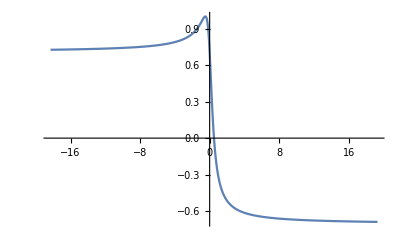

```mathematica
Plot[(1-2 x)/(√(2+8 x^2)),{x,-18.30666666666667,19.30666666666667}]
```

```mathematica
LaplaceTransform[f[x],x,u]
```

LaplaceTransform[f[x],x,u]

```mathematica
TraditionalForm[LaplaceTransform[f[x],x,u]]
```

ℒ_x[f(x)](u)

```mathematica
Integrate[f[x]Exp[-s x],x]
```

∫ⅇ^(-s x) f[x]ⅆx

```mathematica
Integrate[f[x]Exp[-s x],x]
```

∫ⅇ^(-s x) f[x]ⅆx

```mathematica
Integrate[f[s]Exp[-s x],x]
```

-(ⅇ^(-s x) f[s])/s

```mathematica
Integrate[x Exp[-s x],x]
```

-(ⅇ^(-s x) (1+s x))/s^2

```mathematica
Manipulate[Plot[-(ⅇ^(-s x) (1+s x))/s^2,{x,-2.8177895355745477,2.8177895355745477}],{s,-2.8177895355745477,2.8177895355745477}]
```

```mathematica
Integrate[x Exp[-s x],{x,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(-s x) x does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-s x) xⅆx

```mathematica
Integrate[Exp[x] Exp[-s x],{x,-∞,∞}]
```

Integrate::idiv: Integral of ⅇ^(x-s x) does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(x-s x)ⅆx